# Number of matchings of a max clique compared to any subgraphs

n is the dimension of the graph

```mathematica
n=10
```

10

```mathematica
NumberPerfectMatchings[graph_]:=
Module[{lg},lg=LineGraph[graph];Length[EdgeList[graph][[#]]&/@FindIndependentVertexSet[lg,Length/@FindIndependentVertexSet[lg],All]]]
```

```mathematica
RandomSubgraph[g_?GraphQ,s_]:=Subgraph[g,RandomSample[VertexList[g],s]]
```

RandomInteger::udist: The specification Integer[45.] is not a random distribution recognized by the system.

```mathematica
AverageMatchingNumber[graph_,N_]:=Module[{vert,tot},vert=VertexCount[graph];tot=0;Do[tot=tot+NumberPerfectMatchings[RandomSubgraph[graph,RandomInteger[vert]]],N];tot/N]
```

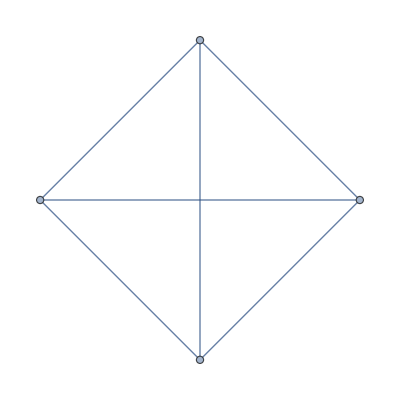

-Graphics-

3

3



0

```mathematica
graph=RandomGraph[{4,6}]

clique=Subgraph[graph,FindClique[graph]]
NumberPerfectMatchings[graph]
NumberPerfectMatchings[clique]
RandomSubgraph[graph,3]
tot=0
Do[tot=NumberPerfectMatchings[RandomSubgraph[graph,RandomInteger[3]]],10]
```

```mathematica
AverageMatchingNumber[graph,2]
```